# Description of Activation Functions

## Grid

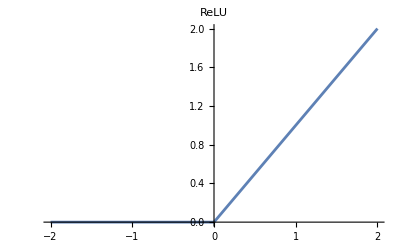
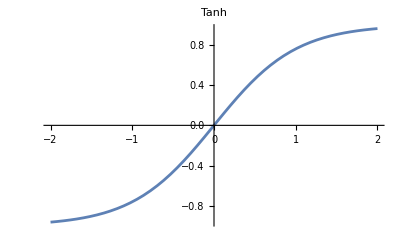
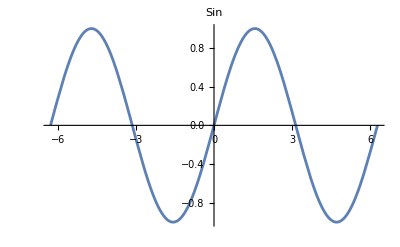
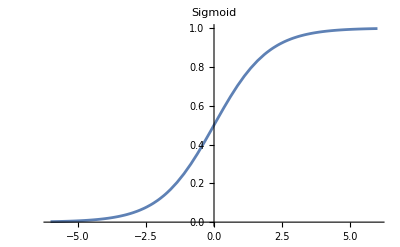
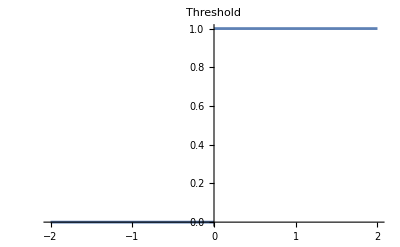
Activation Function | Formula | Graph | Description
Ramp (ReLU) | f(x) = Max[0, x] | -Graphics- | Ramp outputs zero for negative values and zero, but outputs x for positive values, making it a piecewise linear function.
Tanh | f(x) = Tanh[x] | -Graphics- | Tanh takes inputs and maps them to the range (-1, 1), and it's symmetric around the origin, so negative inputs produce negative outputs and positive inputs produce positive outputs.
Sin | f(x) = Sin[x] | -Graphics- | Sin outputs sin(x) for any input x.
Sigmoid | f(x) = 1 / (1 + Exp[-x]) | -Graphics- | Sigmoid is very similar to tanh in shape, but the key difference is that it maps input values to the range (0, 1) instead.
Threshold | f(x) = If[x > 0, 1, 0] | -Graphics- | The thresholding function I've defined here outputs 1 if the input is positive and 0 otherwise.

```mathematica
Grid[{{"Activation Function","Formula","Graph","Description"},{"Ramp (ReLU)","f(x) = Max[0, x]",Plot[Max[0,x],{x,-2,2},PlotLabel->"ReLU"],"Ramp outputs zero for negative values and zero, but outputs x for positive values, making it a piecewise linear function."},{"Tanh","f(x) = Tanh[x]",Plot[Tanh[x],{x,-2,2},PlotLabel->"Tanh"],"Tanh takes inputs and maps them to the range (-1, 1), and it's symmetric around the origin, so negative inputs produce negative outputs and positive inputs produce positive outputs."},{"Sin","f(x) = Sin[x]",Plot[Sin[x],{x,-2 Pi,2 Pi},PlotLabel->"Sin"],"Sin outputs sin(x) for any input x."},{"Sigmoid","f(x) = 1 / (1 + Exp[-x])",Plot[1/(1+Exp[-x]),{x,-6,6},PlotLabel->"Sigmoid"],"Sigmoid is very similar to tanh in shape, but the key difference is that it maps input values to the range (0, 1) instead."},{"Threshold","f(x) = If[x > 0, 1, 0]",Plot[If[x>0,1,0],{x,-2,2},PlotLabel->"Threshold"],"The thresholding function I've defined here outputs 1 if the input is positive and 0 otherwise."}},Frame->All,Alignment->{Center,Center}]
```

## Explanation

The grid above gives a brief description of the activation functions this project will use, along with their graphs and formulas. It’s important to note that some of these functions are piecewise linear, while others are non-linear, and that some functions have the ability to output negative numbers, while others don’t. These characteristics will be very important in the implementation portion of this paper, as they will largely dictate the behavior of the neural network.